```mathematica
tasks = {
	Sin[2*x^3]^2/x^3
	, (x^2 - 4)*Sin[(Pi*(x^2))/6] / (x^2 - 1)
	, Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x)
	, 1/2 * Log[Sqrt[x^2 + 1] / Sqrt[x^2 - 1]] - 15*x^2
	, (x^3 - x^2 - x + 1)^(1/3) / Tan[x]
	, 2*Log[(x - 1) / x] + 1
	, Log[x - 1] / (x - 1)^2
}

getVariantForNumber[number_, variationsQuo_]:=(
	Module[{t},
		t = Mod[number , variationsQuo];
		If[t ≠ 0
				, t
				, variationsQuo
			]
	]
);

(* Проверяем, что все графики строятся нормально *)
Table[Plot[tasks[[i]], {x, -10, 10}], {i, 1, Length[tasks]}]

yourNumber := 24  (*сюда вбить ваш номер по списку в рейтинге *)
numberOfYourTask = getVariantForNumber[yourNumber, Length[tasks]]
Print["Номер вашего задания: ", numberOfYourTask]
f[y_]:= tasks[[numberOfYourTask]]/.x->y;
f[x]//TraditionalForm
```

{(Sin[2 x^3]^2)/x^3,((-4+x^2) Sin[(π x^2)/6])/(-1+x^2),(√Abs[-10 x+2 x^2+3 x^3])/(4 x),-15 x^2+1/2 Log[(√(1+x^2))/(√(-1+x^2))],(1-x-x^2+x^3)^(1/3) Cot[x],1+2 Log[(-1+x)/x],Log[-1+x]/(-1+x)^2}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

3

Номер вашего задания: 3

(√Abs[3 x^3+2 x^2-10 x])/(4 x)

```mathematica
(*1.Построить график*)
Plot[
	f[x]
	, {x, -10, 10}
]
```

-Graphics-

```mathematica
(*2.Область определения функции*)
u[x] := 4x
rootsNull := Solve[u[x] == 0, x]
rootsNull
```

{{x→0}}

```mathematica
(*3.Является ли функция четной, нечетной, прочей*)
res1 = f[x] == f[-x] //TautologyQ
res2 = f[x] + f[-x] == 0 //TautologyQ
If[res1, "Функция четная", Null]
If[res2, "Функция нечетная", Null]
If[Not[res1||res2], "Функция прочая", Null]
```

False

False

Функция прочая

```mathematica
(*4.Периодичность функции*)
FunctionPeriod[ Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x), x]
```

0

```mathematica
(*5.Точки пересечения графика с осями координат*)
sols = Solve[f[x]==0, x]
points = {x, 0}/.sols  (*вместо правил замены получаем список точек путем операции подстановки*)
g1 = Plot[f[x], {x, -10, 10}, PlotStyle->Blue];
g2 = ListPlot[points, PlotStyle->{Red, PointSize[Large]}];
Show[{g1, g2}]
Print["Так как x = 0 - точка разрыва, график не пересекается с OY."];
```

{{x→1/3 (-1-√31)},{x→1/3 (-1+√31)}}

{{1/3 (-1-√31),0},{1/3 (-1+√31),0}}

-Graphics-

Так как x = 0 - точка разрыва, график не пересекается с OY.

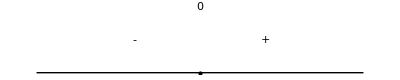

```mathematica
(*6.Промежутки возрастания и убывания*)
(*Смотрим в 'Wolfram - Графики.c' - Graphics[Arrow]*)
Show[
   { Graphics[Line[{{-5, 0}, {5, 0}}]],
        Graphics[Point[{0, 0}, VertexColors->Red]], 
    Graphics[Text["0", {0, 0.8}]], 
          Graphics[Text["+", {2 , 0.4}]],
         Graphics[Text["-", {-2, 0.4}]]
     
 }
]
```

```mathematica
(*7.Точки экстремума и значения в этих точках*)
x = . (* на всякий случай очищаем - нам нужен x только как переменная *)

f = Sqrt[Sqrt[(3*x^3 + 2*x^2 - 10*x)^2]] / (4*x); (* задаём выражение *)
f//TraditionalForm
df = D[f, x]
d2f = D[f,{x, 2}]
```

(((3 x^3+2 x^2-10 x)^2)^(1/4))/(4 x)

((-10+4 x+9 x^2) (-10 x+2 x^2+3 x^3))/(8 x ((-10 x+2 x^2+3 x^3)^2)^(3/4))-(((-10 x+2 x^2+3 x^3)^2)^(1/4))/(4 x^2)

-((-10+4 x+9 x^2) (-10 x+2 x^2+3 x^3))/(4 x^2 ((-10 x+2 x^2+3 x^3)^2)^(3/4))+(((-10 x+2 x^2+3 x^3)^2)^(1/4))/(2 x^3)+(-(3 (-10+4 x+9 x^2)^2 (-10 x+2 x^2+3 x^3)^2)/(4 ((-10 x+2 x^2+3 x^3)^2)^(7/4))+((-10+4 x+9 x^2)^2)/(2 ((-10 x+2 x^2+3 x^3)^2)^(3/4))+((4+18 x) (-10 x+2 x^2+3 x^3))/(2 ((-10 x+2 x^2+3 x^3)^2)^(3/4)))/(4 x)

```mathematica
sols = NSolve[df == 0, x]
g1 = Plot[df, {x, -20, 20}, PlotStyle->Blue,PlotRange -> {{-20, 20}, {-20, 20}}]
g2 = Plot[df, {x, -10, 10}, PlotStyle->Blue,PlotRange -> {{-1, 3}, {-1, 2}}]
g3 = Plot[df, {x, -10, 10}, PlotStyle->Blue,PlotRange -> {{-3, 1}, {-1, 2}}]
```

{{x→0.-1.82574 ⅈ},{x→0.+1.82574 ⅈ}}

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Аналогично и для d2f*)
sols = Solve[d2f == 0, x];
d2f //TraditionalForm
sols//TraditionalForm
g1 = Plot[d2f, {x, -100, 100}, PlotStyle->Blue,PlotRange -> {{-20, 20}, {-10, 10}}]
sols = Table[
	FindRoot[
			d2f == 0
			, {x, i}
		]
	, {i, -3, -0.1}
]
sols1 = Table[
	FindRoot[
			d2f == 0
			, {x, i}
		]
	, {i, 0.1, 2}
]
```

-((9 x^2+4 x-10) (3 x^3+2 x^2-10 x))/(4 x^2 ((3 x^3+2 x^2-10 x)^2)^(3/4))+(((9 x^2+4 x-10)^2)/(2 ((3 x^3+2 x^2-10 x)^2)^(3/4))-(3 (3 x^3+2 x^2-10 x)^2 (9 x^2+4 x-10)^2)/(4 ((3 x^3+2 x^2-10 x)^2)^(7/4))+((18 x+4) (3 x^3+2 x^2-10 x))/(2 ((3 x^3+2 x^2-10 x)^2)^(3/4)))/(4 x)+(((3 x^3+2 x^2-10 x)^2)^(1/4))/(2 x^3)

{{x→√(1/3 (10^(2/3) (31/3)^(1/3)-10))-√(1/3 (-20-10^(2/3) (31/3)^(1/3)-20/(√(3 (10^(2/3) (31/3)^(1/3)-10)))))},{x→√(1/3 (10^(2/3) (31/3)^(1/3)-10))+√(1/3 (-20-10^(2/3) (31/3)^(1/3)-20/(√(3 (10^(2/3) (31/3)^(1/3)-10)))))},{x→-√(1/3 (10^(2/3) (31/3)^(1/3)-10))-1/(√(3/(-20-10^(2/3) (31/3)^(1/3)+20/(√(3 (10^(2/3) (31/3)^(1/3)-10))))))},{x→1/(√(3/(-20-10^(2/3) (31/3)^(1/3)+20/(√(3 (10^(2/3) (31/3)^(1/3)-10))))))-√(1/3 (10^(2/3) (31/3)^(1/3)-10))}}

-Graphics-

{{x→-4.97668×10^18},{x→-1.44594},{x→-1.44594}}

{{x→1.06315},{x→1.06315}}

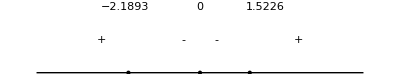

```mathematica
Show[
   { Graphics[Line[{{-5, 0}, {5, 0}}]],
         Graphics[Point[{0, 0}, VertexColors->Red]],
     Graphics[Point[{−2.1893, 0}, VertexColors->Red]], 
     Graphics[Point[{1.5226, 0}, VertexColors->Red]], 
     Graphics[Text["0", {0, 0.8}]],
     Graphics[Text["−2.1893", {-2.3, 0.8}]],
     Graphics[Text["1.5226", {2, 0.8}]],
         Graphics[Text["+", {3 , 0.4}]],
     Graphics[Text["+", {-3 , 0.4}]],
         Graphics[Text["-", {0.5, 0.4}]],
     Graphics[Text["-", {-0.5, 0.4}]]
     
 }
]
```

```mathematica
(*Непрерывность. Наличие точек разрыва и их классификация*)
x = . (* на всякий случай очищаем - нам нужен x только как переменная *)
f = Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x); (* задаём выражение *)
f//TraditionalForm

Print["lim [x -> + 0] f[x] = ", Limit[f, x -> 0, Direction -> "FromAbove"]]
Print["lim [x -> - 0] f[x] = ", Limit[f, x -> 0, Direction -> "FromBelow"]]

(*даст +/- бесконечность
точка разрыва 2 рода в x = 0.
*)
```

(√Abs[3 x^3+2 x^2-10 x])/(4 x)

lim [x -> + 0] f[x] = ∞

lim [x -> - 0] f[x] = -∞

```mathematica
(*9.Асимптоты*)
"Горизонтальных асимптот нет."
Print["lim [x → +Infinity] f[x] = ", Limit[f, x -> +Infinity]]
Print["lim [x → -Infinity] f[x] = ", Limit[f, x -> -Infinity]]

(*График с Асимптотами*)
"Вертикальная асимптота есть."
Show[
    Plot[f, {x, -10, 10}],
    Graphics[{Dashing[{0.02}], Line[{{0, -10}, {0, 10}}]}]
]
```

Горизонтальных асимптот нет.

lim [x → +Infinity] f[x] = ∞

lim [x → -Infinity] f[x] = -∞

Вертикальная асимптота есть.

-Graphics-